## Solve the real equation outside the worldtube

NDSolveValue::precw: The precision of the differential equation ({{-(6 phiF[a])/(Times[«2»]+a)^2-(ⅈ (-48 Power[«2»]+1920 Power[«2»] Power[«2»]) phiF'[a])/(1+Times[«3»])^3+(2 phiF'[a])/((1+Times[«3»]) (Times[«2»]+a))+phiF''[a]/(1+Times[«3»])^2==ⅈ/((-5+ⅈ Power[«2»]+a) π),phiF[9/2]==«59»-«64» ⅈ,phiF'[9/2]==5.397073616826685236239382845+0.0448045230387219447919715848376 ⅈ},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolveValue::precw: The precision of the differential equation ({{-(6 phiR[a])/(Times[«2»]+a)^2-(ⅈ (-48 Power[«2»]+1920 Power[«2»] Power[«2»]) phiR'[a])/(1+Times[«3»])^3+(2 phiR'[a])/((1+Times[«3»]) (Times[«2»]+a))+phiR''[a]/(1+Times[«3»])^2==ⅈ/((-5+Times[«2»]+a) π)+(ⅈ (-48 Power[«2»]+1920 Power[«2»] Power[«2»]) («1»))/(1+Times[«3»])^3-(2 («1»))/((1+Times[«3»]) (Times[«2»]+a))-(«1»)/(1+Times[«3»])^2+(6 («1»))/(Times[«2»]+a)^2,phiR[9/2]==«59»+«76» ⅈ,phiR'[9/2]==«78»-«77» ⅈ},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolveValue::precw: The precision of the differential equation ({{-(6 phi3[a])/a^2+(2 phi3'[a])/a+phi3''[a]==0,phi3[11/2]==18.152410605559721769332452099,phi3'[11/2]==6.6},{},{},{},{}}) is less than WorkingPrecision (30.).

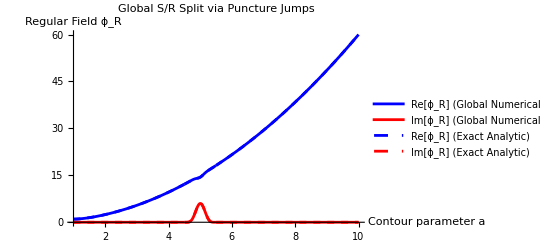

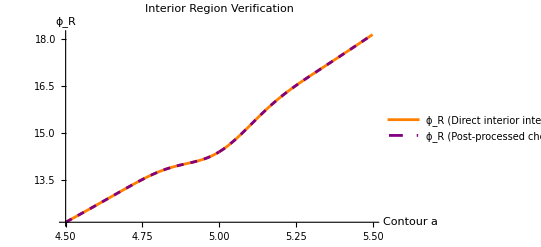

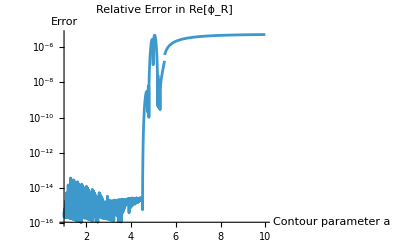

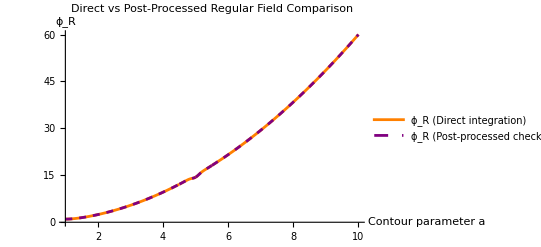

```mathematica
ClearAll["Global`*"]

(* ==========================================1. PARAMETERS& COMPLEX CONTOUR==========================================*)
lMode=2;
r0=5;
(*FIX 1:Must be 12 to prevent interior divergence!*)
order=6;

radius=1/2;
amplitude=1;
aL=r0-radius;
aR=r0+radius;
wp=30;

y[a_]=a+I*(amplitude*(1-((a-r0)/radius)^2)^6);
yPrime[a_]=D[y[a],a];
yDoublePrime[a_]=D[y[a],{a,2}];

(* ==========================================2. AUTOMATED ANALYTIC FIELDS==========================================*)
radialODE[psi_,r_]:=psi''[r]+(2/r)*psi'[r]-(lMode*(lMode+1)/r^2)*psi[r];
complexSource[r_]:=I/(Pi*(r-r0));

generalSingular=DSolveValue[radialODE[ψ,r]==complexSource[r],ψ[r],r];
singularModeExact=generalSingular/. C[_]->0;

phiSLocal[r_]=Normal[Series[singularModeExact,{r,r0,order}]];
homogExact[r_]=DSolveValue[{radialODE[ψ,r]==0,ψ[1]==1,ψ'[1]==0},ψ[r],r];

exactS[r_]=singularModeExact;
exactSPrime[r_]=D[exactS[r],r];

(* ==========================================3. SIMPLIFIED ODE OPERATORS==========================================*)
odeOpReal[u_,a_]:=u''[a]+(2/a)*u'[a]-(lMode*(lMode+1)/a^2)*u[a];

odeOpComplex[u_,a_]:=(1/yPrime[a]^2)*u''[a]-(yDoublePrime[a]/yPrime[a]^3)*u'[a]+(2/y[a])*(1/yPrime[a])*u'[a]-(lMode*(lMode+1)/y[a]^2)*u[a];

localS[a_]=phiSLocal[y[a]];
localSPrime[a_]=D[localS[a],a];
Seff[a_]=complexSource[y[a]]-odeOpComplex[localS,a];

(* ==========================================4. NUMERICAL SOLVE (3-REGION SPLIT)==========================================*)
aMin=1;
aMax=10;

(*---REGION 1:Left Exterior (Strictly Real,Regular Field)---*)
valLInit=N[1,wp];
derLInit=N[0,wp];

sol1=NDSolveValue[{odeOpReal[phi1,a]==0,phi1[aMin]==valLInit,phi1'[aMin]==derLInit},phi1,{a,aMin,aL},WorkingPrecision->wp];

valL=sol1[aL];
derL=sol1'[aL];

(*Evaluate Exact AND Taylor singularities at left boundary*)
exactValL=N[exactS[aL],wp];
exactDerL=N[exactSPrime[aL],wp];
taylorValL=N[localS[aL],wp];
taylorDerL=N[localSPrime[aL],wp];

(*---REGION 2:Interior Worldtube (Complex Contour)---*)
(*1. Full Field inside (must include the exact singularity from Region 1)*)
bc1F=phiF[aL]==valL+exactValL;
bc2F=phiF'[aL]==derL+exactDerL;
solFull2=NDSolveValue[{odeOpComplex[phiF,a]==complexSource[y[a]],bc1F,bc2F},phiF,{a,aL,aR},WorkingPrecision->wp];

(*2. Regular Field inside (match full fields,subtract interior taylor singularity)*)
bc1R=phiR[aL]==valL+exactValL-taylorValL;
bc2R=phiR'[aL]==derL+exactDerL-taylorDerL;
solReg2=NDSolveValue[{odeOpComplex[phiR,a]==Seff[a],bc1R,bc2R},phiR,{a,aL,aR},WorkingPrecision->wp];

(*---REGION 3:Right Exterior (Strictly Real,Regular Field)---*)
valR=solReg2[aR];
derR=solReg2'[aR];

(*Evaluate Exact AND Taylor singularities at right boundary*)
exactValR=N[exactS[aR],wp];
exactDerR=N[exactSPrime[aR],wp];
taylorValR=N[localS[aR],wp];
taylorDerR=N[localSPrime[aR],wp];

(*Reconstruct the real regular field for the right exterior*)
icVal3=Re[valR+taylorValR-exactValR];
icDer3=Re[derR+taylorDerR-exactDerR];

sol3=NDSolveValue[{odeOpReal[phi3,a]==0,phi3[aR]==icVal3,phi3'[aR]==icDer3},phi3,{a,aR,aMax},WorkingPrecision->wp];

(* ==========================================5. STITCH& VISUALIZATION==========================================*)
yGlobal[a_]:=Piecewise[{{a,a<aL},{y[a],a<=aR}},a];

(*1. The Regular Field is just your un-sourced exterior solutions and the interior regular solution*)
phiRegGlobal[a_]:=Piecewise[{{sol1[a],a<aL},{solReg2[a],a<=aR}},sol3[a]];

(*2. The Full Field MUST contain the exact singularity outside to be physically meaningful*)
phiFullGlobal[a_]:=Piecewise[{{sol1[a]+exactS[a],a<aL},{solFull2[a],a<=aR}},sol3[a]+exactS[a]];

(*3. The post-process check subtracts the appropriate singularity from the Full field*)
phiRegularCheck[a_]:=Piecewise[{{phiFullGlobal[a]-exactS[a],a<aL},{phiFullGlobal[a]-localS[a],a<=aR}},phiFullGlobal[a]-exactS[a]];

(*Plot 1:Standard Global Regular Field Comparison*)
Plot[{Re[phiRegGlobal[a]],Im[phiRegGlobal[a]],Re[homogExact[yGlobal[a]]],Im[homogExact[yGlobal[a]]]},{a,aMin,aMax},PlotRange->All,PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},PlotLegends->{"Re[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)] (Global Numerical)","Im[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)] (Global Numerical)","Re[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)] (Exact Analytic)","Im[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)] (Exact Analytic)"},AxesLabel->{"Contour parameter a","Regular Field \!\(\*SubscriptBox[\(ϕ\), \(R\)]\)"},PlotLabel->"Global S/R Split via Puncture Jumps"]

(*Plot 2:Verify Direct Integration vs Post-Processing Subtraction inside Worldtube*)
Plot[{Re[solReg2[a]],Re[solFull2[a]-localS[a]]},{a,aL,aR},PlotStyle->{Orange,{Purple,Dashed}},PlotLegends->{"\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Direct interior integration)","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Post-processed check)"},AxesLabel->{"Contour a","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)"},PlotLabel->"Interior Region Verification"]

(*Plot 3:Absolute Error of the Global Regular Field*)
LogPlot[Abs[(Re[phiRegGlobal[a]]-Re[homogExact[yGlobal[a]]])/Re[phiRegGlobal[a]]],{a,aMin,aMax},PlotLabel->"Relative Error in Re[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)]",AxesLabel->{"Contour parameter a","Error"}]

(*Plot 4:The global check function comparison*)
Plot[{Re[phiRegGlobal[a]],Re[phiRegularCheck[a]]},{a,aMin,aMax},PlotStyle->{Orange,{Purple,Dashed}},PlotLegends->{"\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Direct integration)","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Post-processed check)"},AxesLabel->{"Contour parameter a","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)"},PlotLabel->"Direct vs Post-Processed Regular Field Comparison"]
```

### test

```mathematica
localSource[a_]:=odeOpComplex[localS,a];
```

```mathematica
Series[complexSource[r],{r,r0,order}]
```

ⅈ/(π (r-5))+O[r-5]^7

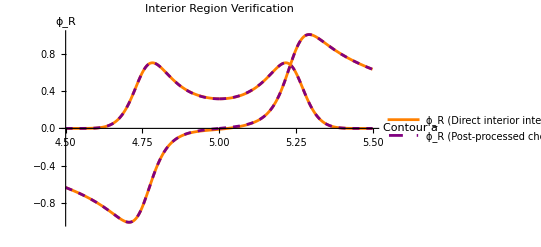

```mathematica
Plot[{Re[localSource[a]],Re[complexSource[y[a]]],Im[localSource[a]],Im[complexSource[y[a]]]},{a,aL,aR},PlotStyle->{Orange,{Purple,Dashed}},PlotLegends->{"\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Direct interior integration)","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Post-processed check)"},AxesLabel->{"Contour a","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)"},PlotLabel->"Interior Region Verification"]
```

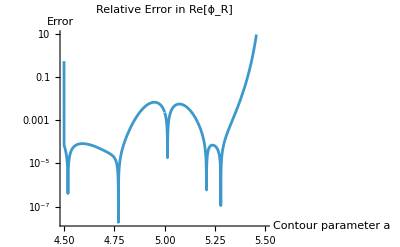

```mathematica
LogPlot[Abs[(Re[localSource[a]]-Re[complexSource[y[a]]])/Re[complexSource[y[a]]]],{a,aL,aR},PlotLabel->"Relative Error in Re[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)]",AxesLabel->{"Contour parameter a","Error"}]
```

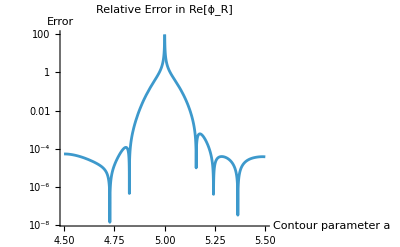

```mathematica
LogPlot[Abs[(Im[localSource[a]]-Im[complexSource[y[a]]])/Im[complexSource[y[a]]]],{a,aL,aR},PlotLabel->"Relative Error in Re[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)]",AxesLabel->{"Contour parameter a","Error"}]
```

## No use of Exact singular field except calculating the expansion

NDSolveValue::precw: The precision of the differential equation ({{-(6 phiF[a])/(Times[«2»]+a)^2-(ⅈ (-48 Power[«2»]+1920 Power[«2»] Power[«2»]) phiF'[a])/(1+Times[«3»])^3+(2 phiF'[a])/((1+Times[«3»]) (Times[«2»]+a))+phiF''[a]/(1+Times[«3»])^2==ⅈ/((-5+ⅈ Power[«2»]+a) π),phiF[9/2]==12.154389574759915419205895785-1.01139509961426925348272289979 ⅈ,phiF'[9/2]==5.397073616826685236239382845+0.044810529830711460250281150942 ⅈ},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolveValue::precw: The precision of the differential equation (…) is less than WorkingPrecision (30.).

NDSolveValue::precw: The precision of the differential equation ({{-(6 phi3[a])/a^2+(2 phi3'[a])/a+phi3''[a]==0,phi3[11/2]==18.152407406461299531674237727,phi3'[11/2]==6.6},{},{},{},{}}) is less than WorkingPrecision (30.).

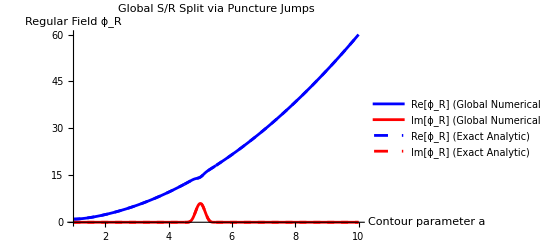

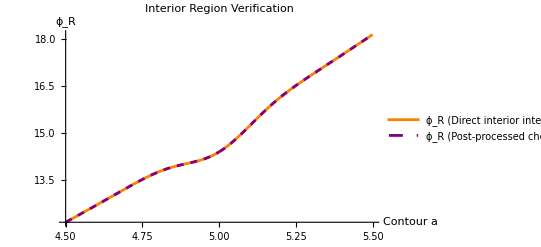

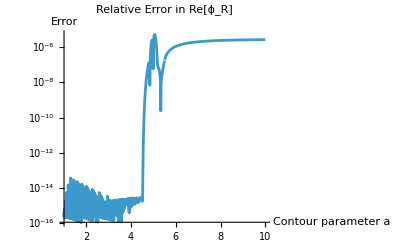

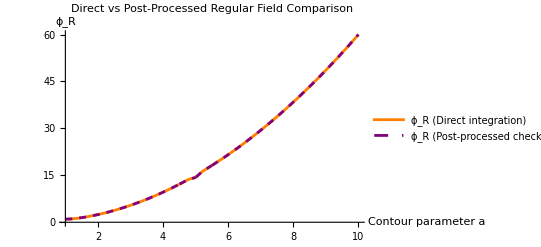

```mathematica
ClearAll["Global`*"]

(* ==========================================1. PARAMETERS& COMPLEX CONTOUR==========================================*)
lMode=2;
r0=5;
(*FIX 1:Must be 12 to prevent interior divergence!*)
order=6;

radius=1/2;
amplitude=1;
aL=r0-radius;
aR=r0+radius;
wp=30;

y[a_]=a+I*(amplitude*(1-((a-r0)/radius)^2)^6);
yPrime[a_]=D[y[a],a];
yDoublePrime[a_]=D[y[a],{a,2}];

(* ==========================================2. AUTOMATED ANALYTIC FIELDS==========================================*)
radialODE[psi_,r_]:=psi''[r]+(2/r)*psi'[r]-(lMode*(lMode+1)/r^2)*psi[r];
complexSource[r_]:=I/(Pi*(r-r0));

generalSingular=DSolveValue[radialODE[ψ,r]==complexSource[r],ψ[r],r];
singularModeExact=generalSingular/. C[_]->0;

phiSLocal[r_]=Normal[Series[singularModeExact,{r,r0,order}]];
homogExact[r_]=DSolveValue[{radialODE[ψ,r]==0,ψ[1]==1,ψ'[1]==0},ψ[r],r];

exactS[r_]=singularModeExact;
exactSPrime[r_]=D[exactS[r],r];

(* ==========================================3. SIMPLIFIED ODE OPERATORS==========================================*)
odeOpReal[u_,a_]:=u''[a]+(2/a)*u'[a]-(lMode*(lMode+1)/a^2)*u[a];

odeOpComplex[u_,a_]:=(1/yPrime[a]^2)*u''[a]-(yDoublePrime[a]/yPrime[a]^3)*u'[a]+(2/y[a])*(1/yPrime[a])*u'[a]-(lMode*(lMode+1)/y[a]^2)*u[a];

localS[a_]=phiSLocal[y[a]];
localSPrime[a_]=D[localS[a],a];
Seff[a_]=complexSource[y[a]]-odeOpComplex[localS,a];

(* ==========================================4. NUMERICAL SOLVE (3-REGION SPLIT)==========================================*)
aMin=1;
aMax=10;

(*---REGION 1:Left Exterior (Strictly Real,Regular Field)---*)
valLInit=N[1,wp];
derLInit=N[0,wp];

sol1=NDSolveValue[{odeOpReal[phi1,a]==0,phi1[aMin]==valLInit,phi1'[aMin]==derLInit},phi1,{a,aMin,aL},WorkingPrecision->wp];

valL=sol1[aL];
derL=sol1'[aL];

(*Evaluate Exact AND Taylor singularities at left boundary*)
taylorValL=N[localS[aL],wp];
taylorDerL=N[localSPrime[aL],wp];

(*---REGION 2:Interior Worldtube (Complex Contour)---*)
(*1. Full Field inside (must include the exact singularity from Region 1)*)
bc1F=phiF[aL]==valL+taylorValL;
bc2F=phiF'[aL]==derL+taylorDerL;
solFull2=NDSolveValue[{odeOpComplex[phiF,a]==complexSource[y[a]],bc1F,bc2F},phiF,{a,aL,aR},WorkingPrecision->wp];

(*2. Regular Field inside (match full fields,subtract interior taylor singularity)*)
bc1R=phiR[aL]==valL;
bc2R=phiR'[aL]==derL;
solReg2=NDSolveValue[{odeOpComplex[phiR,a]==Seff[a],bc1R,bc2R},phiR,{a,aL,aR},WorkingPrecision->wp];

(*---REGION 3:Right Exterior (Strictly Real,Regular Field)---*)
valR=solReg2[aR];
derR=solReg2'[aR];

(*Evaluate Exact AND Taylor singularities at right boundary*)
taylorValR=N[localS[aR],wp];
taylorDerR=N[localSPrime[aR],wp];

(*Reconstruct the real regular field for the right exterior*)
icVal3=Re[valR];
icDer3=Re[derR];

sol3=NDSolveValue[{odeOpReal[phi3,a]==0,phi3[aR]==icVal3,phi3'[aR]==icDer3},phi3,{a,aR,aMax},WorkingPrecision->wp];

(* ==========================================5. STITCH& VISUALIZATION==========================================*)
yGlobal[a_]:=Piecewise[{{a,a<aL},{y[a],a<=aR}},a];

(*1. The Regular Field is just your un-sourced exterior solutions and the interior regular solution*)
phiRegGlobal[a_]:=Piecewise[{{sol1[a],a<aL},{solReg2[a],a<=aR}},sol3[a]];

(*2. The Full Field MUST contain the exact singularity outside to be physically meaningful*)
phiFullGlobal[a_]:=Piecewise[{{sol1[a]+exactS[a],a<aL},{solFull2[a],a<=aR}},sol3[a]+exactS[a]];

(*3. The post-process check subtracts the appropriate singularity from the Full field*)
phiRegularCheck[a_]:=Piecewise[{{phiFullGlobal[a]-exactS[a],a<aL},{phiFullGlobal[a]-localS[a],a<=aR}},phiFullGlobal[a]-exactS[a]];

(*Plot 1:Standard Global Regular Field Comparison*)
Plot[{Re[phiRegGlobal[a]],Im[phiRegGlobal[a]],Re[homogExact[yGlobal[a]]],Im[homogExact[yGlobal[a]]]},{a,aMin,aMax},PlotRange->All,PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},PlotLegends->{"Re[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)] (Global Numerical)","Im[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)] (Global Numerical)","Re[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)] (Exact Analytic)","Im[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)] (Exact Analytic)"},AxesLabel->{"Contour parameter a","Regular Field \!\(\*SubscriptBox[\(ϕ\), \(R\)]\)"},PlotLabel->"Global S/R Split via Puncture Jumps"]

(*Plot 2:Verify Direct Integration vs Post-Processing Subtraction inside Worldtube*)
Plot[{Re[solReg2[a]],Re[solFull2[a]-localS[a]]},{a,aL,aR},PlotStyle->{Orange,{Purple,Dashed}},PlotLegends->{"\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Direct interior integration)","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Post-processed check)"},AxesLabel->{"Contour a","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)"},PlotLabel->"Interior Region Verification"]

(*Plot 3:Absolute Error of the Global Regular Field*)
LogPlot[Abs[(Re[phiRegGlobal[a]]-Re[homogExact[yGlobal[a]]])/Re[phiRegGlobal[a]]],{a,aMin,aMax},PlotLabel->"Relative Error in Re[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)]",AxesLabel->{"Contour parameter a","Error"}]

(*Plot 4:The global check function comparison*)
Plot[{Re[phiRegGlobal[a]],Re[phiRegularCheck[a]]},{a,aMin,aMax},PlotStyle->{Orange,{Purple,Dashed}},PlotLegends->{"\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Direct integration)","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Post-processed check)"},AxesLabel->{"Contour parameter a","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)"},PlotLabel->"Direct vs Post-Processed Regular Field Comparison"]
```

## The Boundary Value Problem (Shooting Method) in a box

NDSolveValue::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (30.).

NDSolveValue::precw: The precision of the differential equation ({{-(6 phi3[a])/a^2+(2 phi3'[a])/a+phi3''[a]==0,phi3[11/2]==18.15240420738167425599665896,phi3'[11/2]==6.6},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolveValue::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (30.).

NDSolveValue::precw: The precision of the differential equation ({{-(6 phi3[a])/a^2+(2 phi3'[a])/a+phi3''[a]==0,phi3[11/2]==24.201202103700248708961299646,phi3'[11/2]==8.8},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolveValue::precw: The precision of the differential equation ({{-(6 phi1[a])/a^2+(2 phi1'[a])/a+phi1''[a]==0,phi1[1]==1.,phi1'[1]==-3.000050000585928752026570894},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolveValue::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (30.).

NDSolveValue::precw: The precision of the differential equation ({{-(6 phi3[a])/a^2+(2 phi3'[a])/a+phi3''[a]==0,phi3[11/2]==0.0057080749870492316976414991,phi3'[11/2]==-0.00339},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolveValue::precw will be suppressed during this calculation.

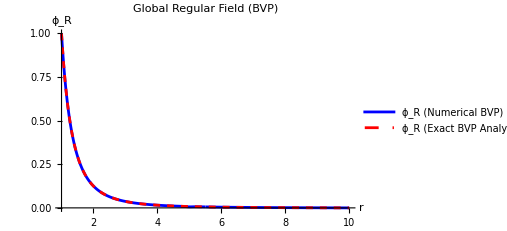

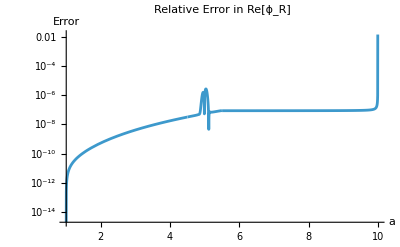

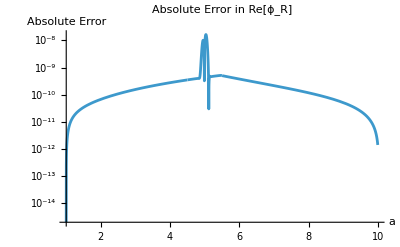

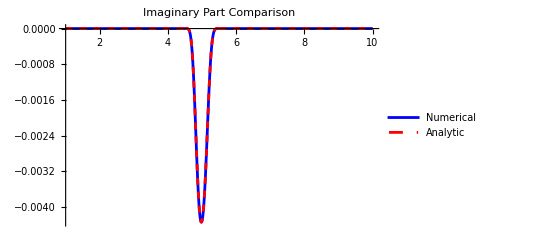

```mathematica
ClearAll["Global`*"]

(* ==========================================1. PARAMETERS& COMPLEX CONTOUR==========================================*)
lMode=2;
r0=5;
order=12;

radius=1/2;
amplitude=1;
aL=r0-radius;
aR=r0+radius;
wp=30;

y[a_]=a+I*(amplitude*(1-((a-r0)/radius)^2)^6);
yPrime[a_]=D[y[a],a];
yDoublePrime[a_]=D[y[a],{a,2}];

(* ==========================================2. AUTOMATED ANALYTIC FIELDS (UPDATED FOR BVP)==========================================*)
radialODE[psi_,r_]:=psi''[r]+(2/r)*psi'[r]-(lMode*(lMode+1)/r^2)*psi[r];
complexSource[r_]:=I/(Pi*(r-r0));

generalSingular=DSolveValue[radialODE[ψ,r]==complexSource[r],ψ[r],r];

(*The Singular Field remains identical (C=0) because it is a LOCAL property*)
singularModeExact=generalSingular/. C[_]->0;
exactS[r_]=singularModeExact;
exactSPrime[r_]=D[exactS[r],r];

phiSLocal[r_]=Normal[Series[singularModeExact,{r,r0,order}]];

(*NEW:The Exact Regular Field must now satisfy our Box Boundary Conditions*)
bcLeftExact=1;
bcRightExact=0;
homogExactBVP[r_]=DSolveValue[{radialODE[ψ,r]==0,ψ[1]==bcLeftExact,ψ[10]==bcRightExact},ψ[r],r];


(* ==========================================3. SIMPLIFIED ODE OPERATORS==========================================*)
odeOpReal[u_,a_]:=u''[a]+(2/a)*u'[a]-(lMode*(lMode+1)/a^2)*u[a];

odeOpComplex[u_,a_]:=(1/yPrime[a]^2)*u''[a]-(yDoublePrime[a]/yPrime[a]^3)*u'[a]+(2/y[a])*(1/yPrime[a])*u'[a]-(lMode*(lMode+1)/y[a]^2)*u[a];

localS[a_]=phiSLocal[y[a]];
localSPrime[a_]=D[localS[a],a];
Seff[a_]=complexSource[y[a]]-odeOpComplex[localS,a];

(* ==========================================4. NUMERICAL SOLVE (EXACT LINEAR SHOOTING)==========================================*)
aMin=1;
aMax=10;

bcLeftVal=N[bcLeftExact,wp];
bcRightVal=N[bcRightExact,wp];

exactValL=N[exactS[aL],wp];
exactDerL=N[exactSPrime[aL],wp];
taylorValL=N[localS[aL],wp];
taylorDerL=N[localSPrime[aL],wp];

exactValR=N[exactS[aR],wp];
exactDerR=N[exactSPrime[aR],wp];
taylorValR=N[localS[aR],wp];
taylorDerR=N[localSPrime[aR],wp];

shoot[p_]:=Module[{s1,valL,derL,bc1R,bc2R,sReg2,valR,derR,icVal3,icDer3,s3},s1=NDSolveValue[{odeOpReal[phi1,a]==0,phi1[aMin]==bcLeftVal,phi1'[aMin]==p},phi1,{a,aMin,aL},WorkingPrecision->wp];
valL=s1[aL];derL=s1'[aL];
bc1R=phiR[aL]==valL+exactValL-taylorValL;
bc2R=phiR'[aL]==derL+exactDerL-taylorDerL;
sReg2=NDSolveValue[{odeOpComplex[phiR,a]==Seff[a],bc1R,bc2R},phiR,{a,aL,aR},WorkingPrecision->wp];
valR=sReg2[aR];derR=sReg2'[aR];
icVal3=Re[valR+taylorValR-exactValR];
icDer3=Re[derR+taylorDerR-exactDerR];
s3=NDSolveValue[{odeOpReal[phi3,a]==0,phi3[aR]==icVal3,phi3'[aR]==icDer3},phi3,{a,aR,aMax},WorkingPrecision->wp];
{s1,sReg2,s3}];

(*FIX:Pass high-precision floats to the shooter to prevent ndnum/ndin errors!*)
funcs0=shoot[N[0,wp]];
valAtMax0=funcs0[[3]][aMax];

funcs1=shoot[N[1,wp]];
valAtMax1=funcs1[[3]][aMax];

correctDeriv=(bcRightVal-valAtMax0)/(valAtMax1-valAtMax0)*(N[1,wp]-N[0,wp])+N[0,wp];

{sol1,solReg2,sol3}=shoot[correctDeriv];


(* ==========================================5. STITCH& VISUALIZATION==========================================*)
yGlobal[a_]:=Piecewise[{{a,a<aL},{y[a],a<=aR}},a];

phiRegGlobal[a_]:=Piecewise[{{sol1[a],a<aL},{solReg2[a],a<=aR}},sol3[a]];
phiFullGlobal[a_]:=Piecewise[{{sol1[a]+exactS[a],a<aL},{solFull2[a],a<=aR}},sol3[a]+exactS[a]];

(*Notice we compare against homogExactBVP[a] now!*)
Plot[{Re[phiRegGlobal[a]],Re[homogExactBVP[a]]},{a,aMin,aMax},PlotRange->All,PlotStyle->{Blue,{Red,Dashed}},PlotLegends->{"\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Numerical BVP)","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\) (Exact BVP Analytic)"},AxesLabel->{"r","\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)"},PlotLabel->"Global Regular Field (BVP)"]

LogPlot[Abs[(Re[phiRegGlobal[a]]-Re[homogExactBVP[yGlobal[a]]])/Re[phiRegGlobal[a]]],{a,aMin,aMax},PlotLabel->"Relative Error in Re[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)]",AxesLabel->{"a","Error"}, PlotRange->All]

LogPlot[Abs[Re[phiRegGlobal[a]]-Re[homogExactBVP[yGlobal[a]]]],{a,aMin,aMax},PlotLabel->"Absolute Error in Re[\!\(\*SubscriptBox[\(ϕ\), \(R\)]\)]",AxesLabel->{"a","Absolute Error"}, PlotRange->All]

Plot[{Im[phiRegGlobal[a]],Im[homogExactBVP[yGlobal[a]]]},{a,aMin,aMax},PlotRange->All,PlotStyle->{Blue,{Red,Dashed}},PlotLegends->{"Numerical","Analytic"},PlotLabel->"Imaginary Part Comparison"]
```